# Neural Networks for Images

From Wolfram Conference 2018: Neural Networks for Images.

## Data

MINIST

```mathematica
ExampleData[{"MachineLearning","MNIST"},"Properties"]
```

{Data,Description,Data,Dimensions,LearningTask,LongDescription,MissingData,Name,Source,TestData,TrainingData,VariableDescriptions,VariableTypes}

```mathematica
ExampleData[{"MachineLearning","MNIST"},"Data"]//Short
```

{-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,«69972»,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9}

```mathematica
ExampleData[{"MachineLearning","MNIST"},"TestData"]//Short
```

{-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,«9972»,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9}

```mathematica
trainData=ExampleData[{"MachineLearning","MNIST"},"Data"];
testData=ExampleData[{"MachineLearning","MNIST"},"TestData"];
```

## Classifier

```mathematica
classifier=NetChain[{
ConvolutionLayer[16,6,"Stride"->2],Ramp,
ConvolutionLayer[32,6,"Stride"->2],Ramp,
FlattenLayer[],
LinearLayer[256],Ramp,
LinearLayer[10],SoftmaxLayer[]
},
"Input"->NetEncoder[{"Image",{28,28},"Grayscale","MeanImage"->0.5}],
"Output"->NetDecoder[{"Class",Range[0,9]}]
]
```

NetChain[<>]

```mathematica
result=NetTrain[classifier,trainData,All,ValidationSet->testData]
```

NetTrain Results
summary | ,,  batches:87500  rounds:10  time:54min  examples/s:216
data | ,,  training examples:70000  validation examples:10000  processed examples:700000  skipped examples:0
method | ,,  ADAMoptimizer  batch size8CPU
round | ,,  loss:1.6×10^-2  error:0.401%
validation | ,,  loss:5.16×10^-3  error:0.170%
 | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
classifier=result["TrainedNet"]
```

NetChain[<>]

```mathematica
(#->classifier[#]&)/@Keys@RandomSample[testData,20]
```

{-Graphics-→1,-Graphics-→4,-Graphics-→2,-Graphics-→0,-Graphics-→4,-Graphics-→3,-Graphics-→1,-Graphics-→6,-Graphics-→8,-Graphics-→5,-Graphics-→9,-Graphics-→1,-Graphics-→4,-Graphics-→2,-Graphics-→7,-Graphics-→3,-Graphics-→4,-Graphics-→9,-Graphics-→3,-Graphics-→6}

```mathematica
Export["minist_classifier.wlnet",classifier]
```

## Generators

```mathematica
generator=NetChain[{
UnitVectorLayer[10],
LinearLayer[256],Ramp,
LinearLayer[512],Ramp,
ReshapeLayer[{32,4,4}],
DeconvolutionLayer[16,6,"Stride"->2],Ramp,
DeconvolutionLayer[1,6,"Stride"->2],LogisticSigmoid},
"Input"->NetEncoder[{"Class",Range[0,9]}],
"Output"->NetDecoder[{"Image","Grayscale"}]
]
```

NetChain[<>]

```mathematica
result=NetTrain[generator,Reverse[trainData,2],All,ValidationSet->Reverse[testData,2]]
```

NetTrain Results
summary | ,,  batches:10940  rounds:10  time:29min  examples/s:400
data | ,,  training examples:70000  validation examples:10000  processed examples:700160  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.21×10^-1  error:10.7%
validation | ,,  loss:2.19×10^-1  error:10.6%
 | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
generator=result["TrainedNet"]
```

NetChain[<>]

```mathematica
{#->generator[#]}&/@Range[0,9]
```

{{0→-Graphics-},{1→-Graphics-},{2→-Graphics-},{3→-Graphics-},{4→-Graphics-},{5→-Graphics-},{6→-Graphics-},{7→-Graphics-},{8→-Graphics-},{9→-Graphics-}}

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"minist_generator.wlnet"},generator]
```

## Auto-Encoder

Auto - encoders attempt to reproduce an incoming images while trying to convey the necessary information through a bottleneck.

```mathematica
noise[σ_]:=(img↦List@Clip[ImageData[img]+RandomReal[NormalDistribution[0,σ],ImageDimensions[img]],{0,1}])
```

```mathematica
latentDim=5;
```

```mathematica
autoEncoder=NetGraph[<|
"encoder"->{
ConvolutionLayer[16,6,"Stride"->2],Ramp,
ConvolutionLayer[32,6,"Stride"->2],Ramp,
FlattenLayer[],
LinearLayer[256],BatchNormalizationLayer[],Ramp,
LinearLayer[latentDim]
},
"decoder"->{
LinearLayer[256],Ramp,
LinearLayer[512],Ramp,
ReshapeLayer[{32,4,4}],
DeconvolutionLayer[16,6,"Stride"->2],Ramp,
DeconvolutionLayer[1,6,"Stride"->2],LogisticSigmoid
},
"loss"->CrossEntropyLossLayer["Binary"]
|>,
{NetPort["NoisyInput"]->"encoder"->"decoder"->NetPort["Output"],
"decoder"->NetPort["loss","Input"],
NetPort["Input"]->NetPort["loss","Target"]},
"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}],
"NoisyInput"->NetEncoder[{"Function",noise[0.5],{1,28,28}}],
"Output"->NetDecoder[{"Image","Grayscale"}]
]
```

NetGraph[<>]

```mathematica
result=NetTrain[autoEncoder,
<|"Input"->Keys[trainData],"NoisyInput"->Keys[trainData]|>,All,
LossFunction->"Loss",
ValidationSet-><|"Input"->Keys[testData],"NoisyInput"->Keys[testData]|>,
MaxTrainingRounds->24
]
```

NetTrain Results
summary | ,,  batches:23249  rounds:22  time:2.9h  examples/s:144
data | ,,  training examples:70000  validation examples:10000  processed examples:1487936  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.39×10^-1  error:5.68%
validation | ,,  loss:1.35×10^-1  error:5.46%
 | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
autoEncoder=result["TrainedNet"]
```

NetGraph[<>]

```mathematica
encoder=NetReplacePart[NetExtract[autoEncoder,"encoder"],"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]]
```

NetChain[<>]

```mathematica
decoder=NetTake[autoEncoder,{"decoder",NetPort["Output"]}]
```

NetGraph[<>]

```mathematica
reconstructor=decoder@*encoder
```

NetGraph[<>]@*NetChain[<>]

```mathematica
samples=Keys@RandomSample[testData,20]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
noisy=ImageEffect[#,{"GaussianNoise",0.5}]&/@samples
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
recover=reconstructor/@noisy
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"minist_autoEncoder.wlnet"},autoEncoder]
```

## Transfer Learning

One can reuse network layers that encode features in another network which is dealing with similar data, thus, requiring less training data.

```mathematica
classifyLayers=NetChain[{Ramp,DropoutLayer[],LinearLayer[10],SoftmaxLayer[]},"Input"->{256}]
```

NetChain[<>]

Substitute classifier layers in the previous encoder

```mathematica
classifier2=NetReplacePart[
NetAppend[
NetTake[encoder,{1,6}],
NetInitialize@classifyLayers],
"Output"->NetDecoder[{"Class",Range[0,9]}]
]
```

NetChain[<>]

Retrain only the classifier layers on a small (just 2%) training set

```mathematica
result=NetTrain[classifier2,RandomSample[trainData,1000],All,
ValidationSet->testData,
LearningRateMultipliers->{1|2|3|4|5|6->0,_->1},
MaxTrainingRounds->500
]
```

NetTrain Results
summary | ,,  batches:8000  rounds:500  time:40min  examples/s:212
data | ,,  training examples:1000  validation examples:10000  processed examples:512000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:6.15×10^-2  error:2.54%
validation | ,,  loss:3.03×10^-1  error:4.41%
 | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
classifier2=result["TrainedNet"]
```

NetChain[<>]

```mathematica
(#->classifier2[#]&)/@Keys@RandomSample[testData,20]
```

{-Graphics-→6,-Graphics-→0,-Graphics-→8,-Graphics-→0,-Graphics-→0,-Graphics-→8,-Graphics-→6,-Graphics-→0,-Graphics-→1,-Graphics-→8,-Graphics-→3,-Graphics-→6,-Graphics-→9,-Graphics-→2,-Graphics-→3,-Graphics-→0,-Graphics-→6,-Graphics-→7,-Graphics-→1,-Graphics-→5}

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"minist_transfer_classifier.wlnet"},classifier2]
```

## Variational Auto-Encoder

Variational auto-encoders (VAEs) are a deep learning technique for obtaining well-structured, latent representations by imposing a uncorrelated, multi-dimensional Gaussian distribution on the latent variables.

```mathematica
latentDim=2;
imageDims={1,28,28};
```

```mathematica
decoder=NetChain[{
LinearLayer[2Times@@imageDims],
ReshapeLayer[imageDims{32,1/4,1/4}],
Ramp,DeconvolutionLayer[16,4,"Stride"->2,"PaddingSize"->1],
Ramp,DeconvolutionLayer[1,4,"Stride"->2,"PaddingSize"->1],
LogisticSigmoid
}]
```

NetChain[<>]

```mathematica
encoder=NetGraph[{
ConvolutionLayer[16,4,"Stride"->2,"PaddingSize"->1],Ramp,
ConvolutionLayer[32,4,"Stride"->2,"PaddingSize"->1],Ramp,
FlattenLayer[],LinearLayer[],LinearLayer[]},
{NetPort["image"]->1->2->3->4->5,
5->6->NetPort["mean"],
5->7->NetPort["log_std"]}
]
```

NetGraph[<>]

```mathematica
zGenerator=NetGraph[{Exp,Times,TotalLayer[]},
{NetPort["log_std"]->1->2,
NetPort["random"]->2,
NetPort["mean"]->3,
2->3->NetPort["z"]}
]
```

NetGraph[<>]

```mathematica
generationLoss=MeanSquaredLossLayer[];
```

```mathematica
latentLoss=NetGraph[{
ThreadingLayer[{mean,logStD}↦mean^2+Exp[logStD]^2-2logStD-1],
SummationLayer[],
ElementwiseLayer[sum↦sum/2]},
{{NetPort["mean"],NetPort["log_std"]}->1,
1->2->3->NetPort["latent_loss"]}]
```

NetGraph[<>]

```mathematica
VAEnet=NetGraph[<|
"encoder"->encoder,
"z_generator"->zGenerator,
"decoder"->decoder,
"generation_loss"->generationLoss,
"latent_loss"->latentLoss
|>,
{NetPort["Input"]->"encoder",
NetPort["encoder","mean"]->NetPort["latent_loss","mean"],
NetPort["encoder","log_std"]->NetPort["latent_loss","log_std"],
NetPort["encoder","mean"]->NetPort["z_generator","mean"],
NetPort["encoder","log_std"]->NetPort["z_generator","log_std"],
NetPort["Random"]->NetPort["z_generator","random"],
"z_generator"->"decoder"->NetPort["Output"],
NetPort["Input"]->NetPort["generation_loss","Target"],
"decoder"->NetPort["generation_loss","Input"],
"generation_loss"->NetPort["generation_loss"]
},
"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}],
"Random"->With[{latentDim=latentDim},NetEncoder[{"Function",RandomReal[NormalDistribution[],{latentDim}]&,{latentDim}}]],
"Output"->NetDecoder[{"Image","Grayscale"}]
]
```

NetGraph[<>]

```mathematica
trainDataVAE=<|"Input"->Keys@trainData,"Random"->ConstantArray[0,Length[trainData]]|>;
```

```mathematica
result=NetTrain[VAEnet,trainDataVAE,All,
LossFunction->{"latent_loss"->Scaled[1],"generation_loss"->Scaled[28*28]},
MaxTrainingRounds->100,
TrainingProgressReporting->"Panel",
BatchSize->64,
Method->{"ADAM","LearningRate"->0.0005}
]
```

NetTrain Results
summary | ,,  batches:109400  rounds:100  time:7.4h  examples/s:261
data | ,,  training examples:70000  processed examples:7001600  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:3.69×10^1  latent_loss:4.56  generation_loss:3.24×10^1
 | 
 |

```mathematica
VAEnet=result["TrainedNet"]
```

NetGraph[<>]

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"minist_VAEnet.wlnet"},VAEnet]
```

Extracting the encoder/decoder

```mathematica
encoder=NetReplacePart[NetExtract[VAEnet,"encoder"],"image"->NetEncoder[{"Image",Rest[imageDims],"Grayscale"}]]
```

NetGraph[<>]

```mathematica
decoder=NetReplacePart[NetExtract[VAEnet,"decoder"],"Output"->NetDecoder["Image"]]
```

NetChain[<>]

Display latent space:

```mathematica
sampDigits=Range[0,9]/.Reverse[RandomSample[testData,10*10],2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

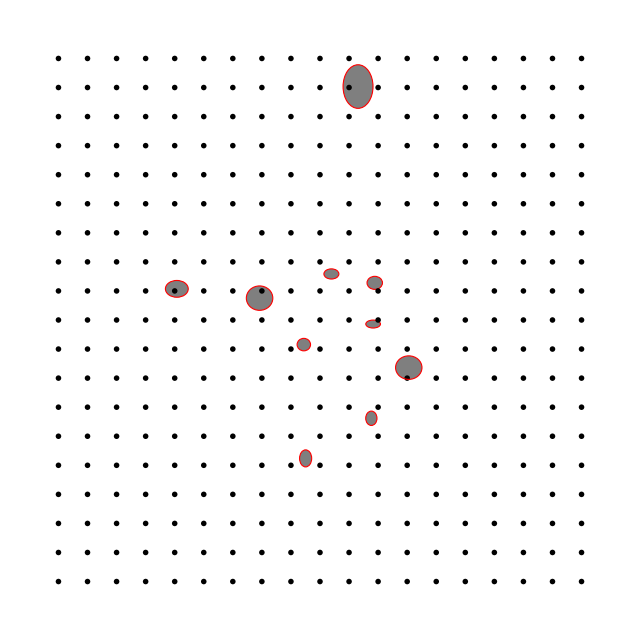

```mathematica
Graphics[Flatten@Table[
Inset[Image[decoder[{x,y}],ImageSize->28],{x,y}],
{x,-3,3,1/3},{y,-3,3,1/3}],
Epilog->{EdgeForm[Red],FaceForm[Opacity[0.5],Red],
Table[Tooltip[Disk["mean",Exp["log_std"]]/.encoder[sampDigits[[k]]],k-1],{k,10}]},
PlotRange->{{-3,3},{-3,3}},ImageSize->640
]
```

Digit interpolation:

```mathematica
Manipulate[Magnify[decoder[{x,y}],4],{x,-2,2},{y,-2,2}]
```

## U-Net

Network with an auto-encoder like structure

O. Ronneberger, P. Fischer, T. Brox “U-Net: Convolutional Networks for Biomedical Image Segmentation,” arXiv:1505.04597 (2015)
(available from https://lmb.informatik.uni-freiburg.de/people/ronneber/u-net/index.html)

```mathematica
net=NetModel["U-Net Trained on Glioblastoma-Astrocytoma U373 Cells on a Polyacrylamide Substrate Data"]
```

## Generative Adversarial Network (GAN)

GANs: generator has to fool discriminator by creating images from random input that look like real images.

```mathematica
latentDim=2;
imageDims={1,28,28};
```

```mathematica
generator=NetChain[{
LinearLayer[256],Ramp,
LinearLayer[512],Ramp,
ReshapeLayer[{32,4,4}],
DeconvolutionLayer[16,6,"Stride"->2],Ramp,
DeconvolutionLayer[1,6,"Stride"->2],LogisticSigmoid},
"Input"->latentDim
]
```

NetChain[<>]

```mathematica
discriminator=NetChain[{
ConvolutionLayer[16,6,"Stride"->2],Ramp,
ConvolutionLayer[32,6,"Stride"->2],Ramp,
FlattenLayer[],
LinearLayer[256],Ramp,
LinearLayer[1]},
"Input"->imageDims
]
```

NetChain[<>]

Wasserstein GAN

```mathematica
wGAN=NetGraph[<|
"generator"->generator,
"discriminator"->NetChain[{ReshapeLayer[Prepend[imageDims,2]],NetMapOperator[discriminator]}],
"combine"->CatenateLayer[],
"loss"->NetChain[{LinearLayer[1,"Weights"->{{-1,1}},"Biases"->{0}],PartLayer[1]},"Input"->{2,1}]
|>,
{NetPort["Random"]->"generator"->"combine",
NetPort["Input"]->"combine",
"combine"->"discriminator"->"loss"},
"Input"->NetEncoder[{"Image",Rest@imageDims,"Grayscale"}],
"Random"->latentDim
]
```

NetGraph[<>]

```mathematica
trainDataGAN=<|"Random"->RandomReal[{-1,1},{Length[trainData],latentDim(*randomDim*)}],
"Input"->Keys@trainData|>;
```

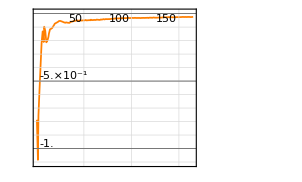
NetTrain Results
summary | ,,  batches:181463  rounds:166  time:11h  examples/s:304
data | ,,  training examples:70000  processed examples:11613632  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:-2.4×10^-2
 | rounds
loss | -Graphics- | 
 |

```mathematica
result=NetTrain[wGAN,trainDataGAN,All,
LossFunction->"Output",
Method->{"ADAM","Beta1"->0.5,"LearningRate"->0.00005,"WeightClipping"->{"discriminator"->0.01}},
LearningRateMultipliers->{"loss"->0,"generator"->-0.2},
BatchSize->64,MaxTrainingRounds->512
]
```

```mathematica
wGAN=result["TrainedNet"]
```

NetGraph[<>]

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"minist_VAEnet.wlnet"},VAEnet]
```

```mathematica
generator=NetExtract[wGAN,"generator"]
```

NetChain[<>]

```mathematica
Table[Image@First@generator[UnitVector[10,k]],{k,10}]
```

## Cyclic GAN

J. Zhu, T. Park, P. Isola, A. A. Efros, “Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks,” arXiv:1703.10593 (2017)
(available from https://github.com/junyanz/CycleGAN)